## TemplateRandomOvalish-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51h (15 June 2017)) loaded Sun 18 Jun 2017 08:47:15
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

There are 500 cells in the tissue.

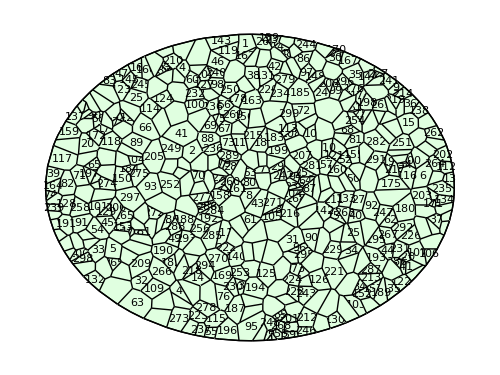

```mathematica
q=TemplateRandomOvalish[500, {100, 75}];
Print["There are ", NTissueCells[q], " cells in the tissue."];  
ShowTissue[q, "CellNumbers"-> True, ImageSize-> 500]
```